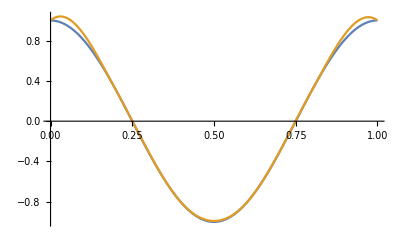

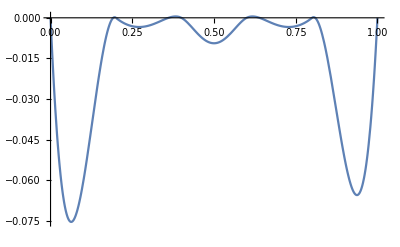

```mathematica
(*Светлана Груева, ФН 81422*)

n=5;

(*дефинираме f(x)*)
f[t_]:=Cos[2*Pi*t];

 (*изчисляваме разстоянието между възлите и самите възли*)
Do[x[k]=k/n,{k,0,n}];
(*разстоянието между всеки 2 възела е едно и също*)
δ=1/n;

(*Коефициентите се изчисляват*)
cа=1/δ;
cb=4/δ;
cc=1/δ;
Do[d[k]=3*(f[x[k]]-f[x[k-1]])/δ^2+3*(f[x[k+1]]-f[x[k]])/δ^2,{k,1,n-1}];

(*Прав ход на прогонката*)
alpha[1]=-cc/cb;
beta[1]=d[1]/cb;

Do[alpha[k]=-cc/(ca*alpha[k-1]+cb),{k,2,n-1}];
Do[beta[k]=(d[k]-ca*beta[k-1])/(ca*alpha[k-1]+cb),{k,2,n-1}];

(*Имаме естествен кубичен сплaйн*)
(*намираме y[0] и y[n] чрез втората производна на инт. полином*)
y[0]=3*(f[x[1]]-f[x[0]])/2*δ - y[1]/2;
y[n]=3*(f[x[n]]-f[x[n-2]])/2*δ - y[n-1]/2;
y[n-1]=beta[n-1];

(*Обратен ход на прогонката*)
Do[y[k]=alpha[k]*y[k+1]+beta[k];,{k,n-2,1,-1}];

Do[a[k]=y[k+1]/δ^2+y[k]/δ^2+2*(f[x[k]]-f[x[k+1]])/δ^3,{k,0,n-1}];
Do[b[k]=(f[x[k+1]]-f[x[k]])/δ^2-y[k]/δ,{k,0,n-1}];

(*общ вид на полиномите,които интерполират f(t) в 2 последователни възела*)
Do[h[k,z_]=a[k]*(z-x[k])^2*(z-x[k+1])+b[k]*(z-x[k])^2+y[k]*(z-x[k])+f[x[k]],{k,0,n-1}];

(*построяване на кубичния сплайн*)
Shelp[i_,t_]:=If[i<=n+1,If[t>=x[i]&&t<x[i+1],h[i,t],Shelp[i+1,t]]];
S[t_]:=Shelp[0,t];

(*визуализация на f(t) и Sn*)
Plot[{f[t],S[t]},{t,0,1},PlotPoints->300]

(*графиката на грешката*)
Plot[f[t]-S[t],{t,0,1},PlotRange->All]
```